```mathematica
(* requires EcoEvo package <https://github.com/cklausme/EcoEvo> -- run this once (ever) to install *)
PacletInstall["https://github.com/cklausme/EcoEvo/raw/master/Paclets/EcoEvo-1.7.2.paclet"]
```

PacletObject[…]

## Set model

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.2 (September 1, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Pop[n1]->{Equation:>(r1-α11 n1-α12 n2)n1},
Pop[n2]->{Equation:>(r2-α21 n1-α22 n2)n2},
Parameters:>{r1>0,r2>0,α11>0,α12>0,α21>0,α22>0}
}];
```

## Analysis

Solve for equilibria:

```mathematica
eq=SolveEcoEq[]
```

{{n1→0,n2→0},{n1→r1/α11,n2→0},{n1→0,n2→r2/α22},{n1→-(-r2 α12+r1 α22)/(α12 α21-α11 α22),n2→-(r2 α11-r1 α21)/(α12 α21-α11 α22)}}

Jacobian matrix:

```mathematica
EcoJacobian[]//MatrixForm
```

(r1-2 n1 α11-n2 α12 | -n1 α12
-n2 α21 | r2-n1 α21-2 n2 α22)

Calculate eigenvalues at each equilibrium:

```mathematica
EcoEigenvalues[eq[[1]]]
```

{r1,r2}

```mathematica
Simplify[EcoEigenvalues[eq[[2]]]]
```

{-r1,r2-(r1 α21)/α11}

```mathematica
Simplify[EcoEigenvalues[eq[[3]]]]
```

{-r2,r1-(r2 α12)/α22}

```mathematica
Simplify[EcoEigenvalues[eq[[4]]]]
```

{-1/(2 α12 α21-2 α11 α22)(r2 α11 α12-r1 α11 α22-r2 α11 α22+r1 α21 α22+√(4 (r2 α11-r1 α21) (r2 α12-r1 α22) (-α12 α21+α11 α22)+(r2 α11 (α12-α22)+r1 (-α11+α21) α22)^2)),1/(2 α12 α21-2 α11 α22)(-r2 α11 α12+r1 α11 α22+r2 α11 α22-r1 α21 α22+√(4 (r2 α11-r1 α21) (r2 α12-r1 α22) (-α12 α21+α11 α22)+(r2 α11 (α12-α22)+r1 (-α11+α21) α22)^2))}

Stability conditions:

```mathematica
EcoStableQ[eq[[1]]]
```

False

```mathematica
FullSimplify[EcoStableQ[eq[[2]]]]
```

Piecewise[{{True, r1 α21>r2 α11}, {False, r1 α21<r2 α11||r1 (α11+α21)<r2 α11}, {Indeterminate, True}}]

```mathematica
FullSimplify[EcoStableQ[eq[[3]]]]
```

Piecewise[{{True, r2 α12>r1 α22}, {False, r1 α22>r2 (α12+α22)||r2 α12<r1 α22}, {Indeterminate, True}}]

```mathematica
FullSimplify[EcoStableQ[eq[[4]]]]
```

Piecewise[{{True, (α12 α21-α11 α22) (r2 α11 (α12-α22)+r1 (-α11+α21) α22)>0&&(r2 α11-r1 α21) (r2 α12-r1 α22) (-α12 α21+α11 α22)<0}, {False, (α12 α21-α11 α22) (r2 α11 (α12-α22)+r1 (-α11+α21) α22)<0||(r2 α11-r1 α21) (r2 α12-r1 α22) (-α12 α21+α11 α22)>0}, {Indeterminate, True}}]

Invasion rates:

```mathematica
λ21=Inv[eq[[2]],n2]
```

r2-(r1 α21)/α11

```mathematica
λ12=Inv[eq[[3]],n1]
```

r1-(r2 α12)/α22

## Numerical examples

### Case I - 1 outcompetes 2

```mathematica
r1=1.2;r2=1;
α11=1;α22=1;
α12=1;α21=1;
```

```mathematica
eq=SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.2,n2→0},{n1→0,n2→1.}}

```mathematica
EcoEigenvalues[eq]
```

{{1.2,1.},{-1.2,-0.2},{-1.,0.2}}

```mathematica
NumberedGridForm[eq,EcoEigenvalues[eq],Header->True]
```

# | eq | EcoEigenvalues[eq]
1 | {n1→0,n2→0} | {1.2,1.}
2 | {n1→1.2,n2→0} | {-1.2,-0.2}
3 | {n1→0,n2→1.} | {-1.,0.2}

```mathematica
λ12=Inv[eq[[3]],n1]
λ21=Inv[eq[[2]],n2]
```

0.2

-0.2

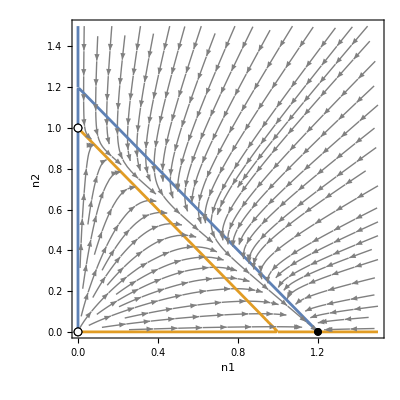

```mathematica
pp=PlotEcoPhasePlane[{n1,0,1.5},{n2,0,1.5}]
```

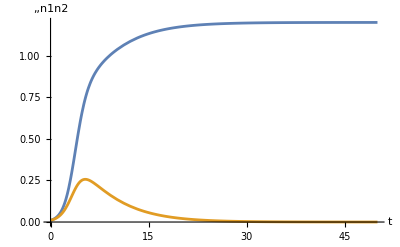

```mathematica
sol=EcoSim[{n1->0.01,n2->0.01},50];
PlotDynamics[sol]
```

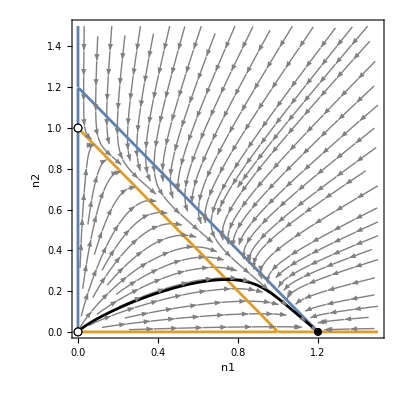

```mathematica
Show[pp,PlotTrajectory[sol,PlotStyle->Black]]
```

### Case III - 1 & 2 coexist

```mathematica
r1=1;r2=1;
α11=1;α22=1;
α12=0.5;α21=0.5;
```

```mathematica
eq=SolveEcoEq[];
NumberedGridForm[eq,EcoEigenvalues[eq],Header->True]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

# | eq | EcoEigenvalues[eq]
1 | {n1→0,n2→0} | {1.,1.}
2 | {n1→1.,n2→0} | {-1.,0.5}
3 | {n1→0,n2→1.} | {-1.,0.5}
4 | {n1→0.666667,n2→0.666667} | {-1.,-0.333333}

```mathematica
λ12=Inv[eq[[3]],n1]
λ21=Inv[eq[[2]],n2]
```

0.5

0.5

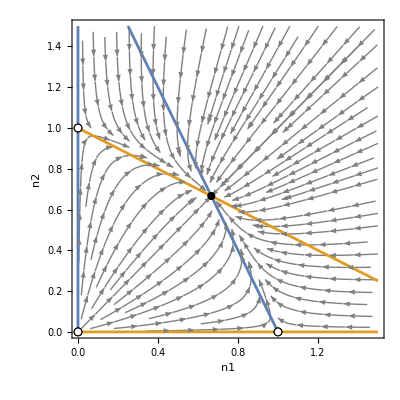

```mathematica
pp=PlotEcoPhasePlane[{n1,0,1.5},{n2,0,1.5}]
```

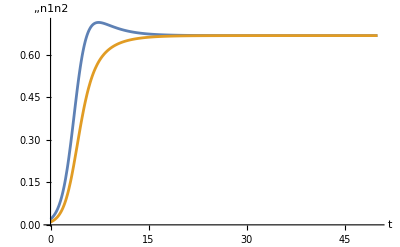

```mathematica
sol=EcoSim[{n1->0.02,n2->0.01},50];
PlotDynamics[sol]
```

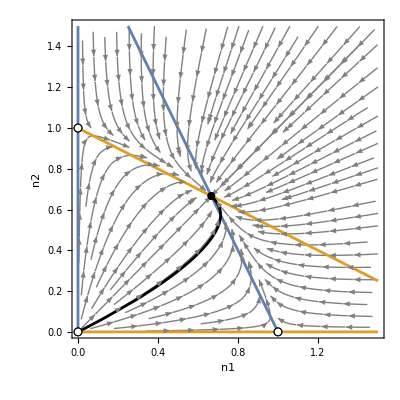

```mathematica
Show[pp,PlotTrajectory[sol,PlotStyle->Black]]
```

### Case IV - 1 or 2 wins (founder control)

```mathematica
r1=1;r2=1;
α11=1;α22=1;
α12=2;α21=2;
```

```mathematica
eq=SolveEcoEq[];
NumberedGridForm[eq,EcoEigenvalues[eq],Header->True]
```

# | eq | EcoEigenvalues[eq]
1 | {n1→0,n2→0} | {1,1}
2 | {n1→1,n2→0} | {-1,-1}
3 | {n1→0,n2→1} | {-1,-1}
4 | {n1→1/3,n2→1/3} | {-1,1/3}

```mathematica
λ12=Inv[eq[[3]],n1]
λ21=Inv[eq[[2]],n2]
```

-1

-1

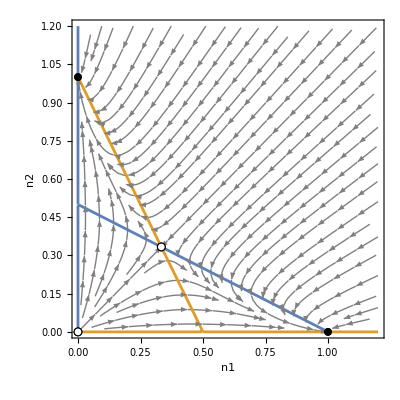

```mathematica
pp=PlotEcoPhasePlane[{n1,0,1.2},{n2,0,1.2}]
```

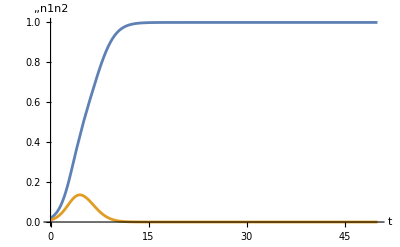

```mathematica
sol=EcoSim[{n1->0.02,n2->0.01},50];
PlotDynamics[sol]
```

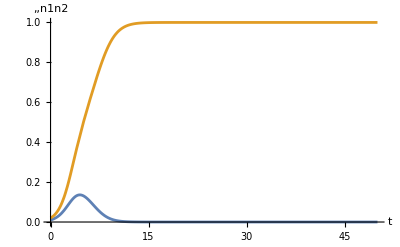

```mathematica
sol2=EcoSim[{n1->0.01,n2->0.02},50];
PlotDynamics[sol2]
```

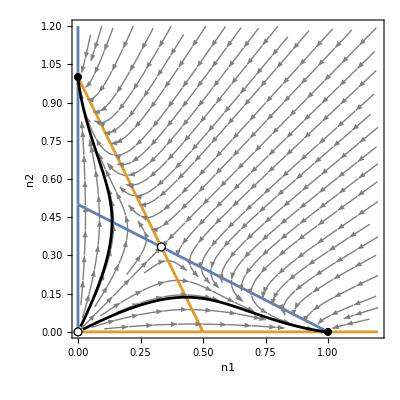

```mathematica
Show[pp,PlotTrajectory[{sol,sol2},PlotStyle->Black]]
```

### Case 0 - neutrality

```mathematica
r1=1;r2=1;
α11=1;α22=1;
α12=1;α21=1;
```

```mathematica
eq=SolveEcoEq[];
NumberedGridForm[eq,EcoEigenvalues[eq],Header->True]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

# | eq | EcoEigenvalues[eq]
1 | {n1→0,n2→0} | {1,1}
2 | {n2→1-n1} | {-1,0}

```mathematica
λ12=Inv[{n1->0,n2->r2/α22},n1]
λ21=Inv[{n1->r1/α11,n2->0},n2]
```

0

0

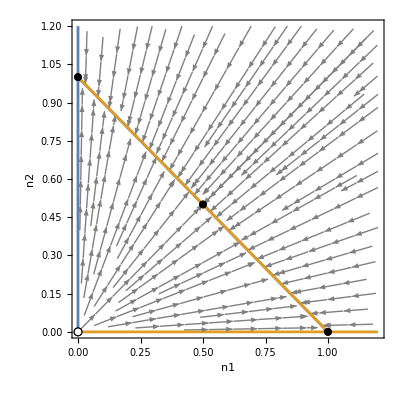

```mathematica
pp=PlotEcoPhasePlane[{n1,0,1.2},{n2,0,1.2}]
```

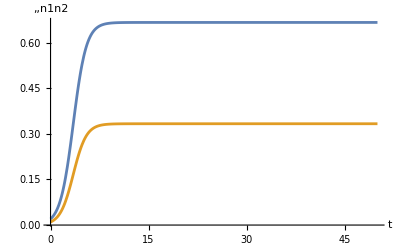

```mathematica
sol=EcoSim[{n1->0.02,n2->0.01},50];
PlotDynamics[sol]
```

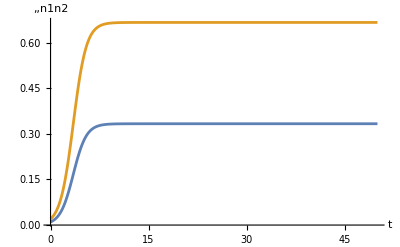

```mathematica
sol2=EcoSim[{n1->0.01,n2->0.02},50];
PlotDynamics[sol2]
```

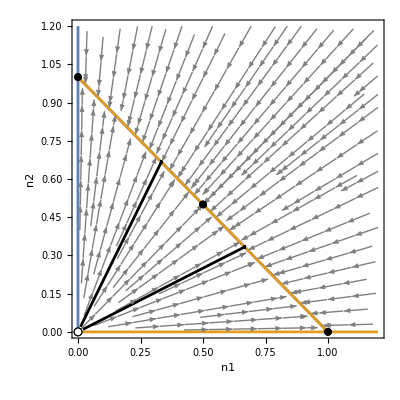

```mathematica
Show[pp,PlotTrajectory[{sol,sol2},PlotStyle->Black]]
```